### Start choosing the example:

```mathematica
t=24;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t];
MFGEquations=DataToEquations[Data];//Timing
v0=MFGEquations["criticalreduced1"][[2]]
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: Done.

{0.5458,Null}

<|j18→1,j19→2,u47→1,j14→1,j15→3,j16→2,j17→3,j20→0,j21→0,j22→0,j23→0,j24→0,j25→0,jt26→0,jt27→1,jt29→1-1,jt30→1-1,jt31→-1+1,jt32→-1+1,jt33→3-1,jt34→0,jt35→2,jt36→3,jt37→0,u41→1,u44→-1+5,u45→-3+4,u46→-2+6,u48→5,u49→6,u39→4,u42→5,u43→6,jt28→1,u38→5,u40→6|>

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort//Values
MFGEquations["criticalreduced2"][[2]]//KeySort//Values
```

{1,3,2,3,1,2,0,0,0,0,0,0,0,1,1,0,0,0,0,2,0,2,3,0,5,4,6,1,5,6,4,1,4,1,5,6}

{1,3,2,3,1,2,0,0,0,0,0,0,0,1,1,0,0,0,0,2,0,2,3,0,5,4,6,1,5,6,4,1,4,1,5,6}

```mathematica
MFGEquations["reduced1"][[2]]//KeySort//Values
MFGEquations["reduced2"][[2]]//KeySort//Values
```

{1,3,2,3,1,2,0,0,0,0,0,0,0,1,1,0,0,0,0,2,0,2,3,0,1,u38,u40,u39,1,u39,1,u38,u40}

{1,3,2,3,1,2,0,0,0,0,0,0,0,1,1,0,0,0,0,2,0,2,3,0,1,u38,u40,u39,1,u39,1,u38,u40}

#### Non-linear case with alpha != 1

```mathematica
Parameters["alpha"]=2;
Parameters
```

<|alpha→2,beta→1,g[m]→Function[{m},m^beta],W[x,A]→Function[{x,A},A Sin[2 π (x+1/4)]^2],V[x]→Function[{x$},W$1034[x$,A]],H[x,p,m]→Function[{x$,p$,m$},p$^2/(2 m$^alpha)+V$1034[x$]-g$1034[m$]]|>

```mathematica
sol1=FixedPoint[FixedSolverStepX1[MFGEquations], MFGEquations["criticalreduced1"][[2]],1, SameTest-> (Norm[(KeySort@#1-KeySort@#2)//Values]<10^(-3)&)]
```

Eliminator: System is not True and Head of system is NOT And or Equal. Returning the input.

Association::incmp: The arguments <|j14→1,j15→3,j16→2,j17→3,j18→1,j19→2,j20→0,j21→0,j22→0,j23→0,j24→0,j25→0,jt26→0,jt27→1,jt28→1,jt29→1-1,jt30→1-1,jt31→-1+1,jt32→-1+1,jt33→3-1,jt34→0,jt35→2,jt36→3,jt37→0,u38→5,u39→4,u40→6,u41→1,u42→5,u43→6,u44→-1+5,u45→-3+4,u46→-2+6,u47→1,u48→5,u49→6|> and <|j14→-1.,j15→-3.,j16→-2.,j17→-3.,j18→-1.,j19→-2.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,j25→0.,jt26→0.,jt27→-1.,«6»,jt34→0.,jt35→-2.,jt36→-3.,jt37→0.,u39→-0.571429,u41→-1,u42→-u38,u43→-u40,u44→1.-1. u38,u45→-1.,u46→-1.-1. u40,u47→-1,u48→-u38,u49→-u40|> in <|j14→1,j15→3,j16→2,j17→3,j18→1,j19→2,j20→0,j21→0,j22→0,j23→0,j24→0,j25→0,jt26→0,jt27→1,jt28→1,jt29→1-1,jt30→1-1,jt31→-1+1,jt32→-1+1,jt33→3-1,jt34→0,jt35→2,jt36→3,jt37→0,u38→5,u39→4,u40→6,u41→1,u42→5,u43→6,u44→-1+5,u45→-3+4,u46→-2+6,u47→1,u48→5,u49→6|>+<|j14→-1.,j15→-3.,j16→-2.,«28»,u47→-1,u48→-u38,u49→-u40|> are incompatible.

Values::invrl: The argument <|j14→-1.,j15→-3.,j16→-2.,j17→-3.,j18→-1.,j19→-2.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,j25→0.,jt26→0.,jt27→-1.,jt28→-1,«5»,jt34→0.,jt35→-2.,jt36→-3.,jt37→0.,u39→-0.571429,u41→-1,u42→-u38,u43→-u40,u44→1.-1. u38,u45→-1.,u46→-1.-1. u40,u47→-1,u48→-u38,u49→-u40|>+<|«1»|> is not a valid Association or a list of rules.

<|j18→1.,j19→2.,u47→1,j14→1.,j15→3.,j16→2.,j17→3.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,j25→0.,jt26→0.,jt27→1.,jt29→1.-1. jt28,jt30→1.-1. jt28,jt31→-1.+1. jt28,jt32→-1.+1. jt28,jt33→3.-1. jt28,jt34→0.,jt35→2.,jt36→3.,jt37→0.,u41→1,u48→u38,u49→u40,u42→u38,u43→u40,u45→0.428571+1. 0.571429,jt28→1,u44→-1.+1. u38,u46→1.+1. u40,u39→0.571429|>

Note that 5 iterations work for the X2 solver tools:

```mathematica
sol2 = FixedPoint[FixedSolverStepX2[MFGEquations], MFGEquations["criticalreduced2"][[2]],3, SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]
<10^(-6)&)]
Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.sol2]
```

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j14-j20-u38+u44==0&&j15-j21-u39+u45==3.42857&&j16-j22-u40+u46==3.

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j14-j20-u38+u44==0&&j15-j21-u39+u45==3.42857&&j16-j22-u40+u46==3.

<|j18→1.,j19→2.,u47→1,j14→1.,j15→3.,j16→2.,j17→3.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,j25→0.,jt26→0.,jt27→1.,jt29→1.-1. 1.,jt30→1.-1. 1.,jt31→-1.+1. 1.,jt32→-1.+1. 1.,jt33→3.-1. 1.,jt34→0.,jt35→2.,jt36→3.,jt37→0.,u41→1,u44→-1.+1. 1.57143,u45→0.428571+1. 0.571429,u46→1.+1. (-0.428571),u48→1.57143,u49→-0.428571,jt28→1.,u38→1.57143,u39→0.571429,u40→-0.428571,u42→1.57143,u43→-0.428571|>

1.13764×10^-15

But if we try one more iteration, the next system is False. Now we have to create a way to deal with this.

```mathematica
sol26It=FixedPoint[FixedSolverStepX2[MFGEquations], MFGEquations["criticalreduced2"][[2]],8, SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#2]
<10^(-6)&)]
Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.%]
```

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j14-j20-u38+u44==0&&j15-j21-u39+u45==3.42857&&j16-j22-u40+u46==3.

<|j18→1.,j19→2.,u47→1,j14→1.,j15→3.,j16→2.,j17→3.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,j25→0.,jt26→0.,jt27→1.,jt29→1.-1. 1.,jt30→1.-1. 1.,jt31→-1.+1. 1.,jt32→-1.+1. 1.,jt33→3.-1. 1.,jt34→0.,jt35→2.,jt36→3.,jt37→0.,u41→1,u44→-1.+1. 1.57143,u45→0.428571+1. 0.571429,u46→1.+1. (-0.428571),u48→1.57143,u49→-0.428571,jt28→1.,u38→1.57143,u39→0.571429,u40→-0.428571,u42→1.57143,u43→-0.428571|>

1.13764×10^-15

```mathematica
sol36It=Catch @ FixedPoint[FixedSolverStepX3[MFGEquations], MFGEquations["criticalreduced2"][[2]],6, SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#2]
<10^(-6)&)]
Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.%]
```

FixedX3: next step: j14-j20-u38+u44==0&&j15-j21-u39+u45==3.42857&&j16-j22-u40+u46==3.

<|j18→1.,j19→2.,u47→1,j14→1.,j15→3.,j16→2.,j17→3.,j20→0.,j21→0.,j22→0.,j23→0.,j24→0.,j25→0.,jt26→0.,jt27→1.,jt29→1.-1. 1.,jt30→1.-1. 1.,jt31→-1.+1. 1.,jt32→-1.+1. 1.,jt33→3.-1. 1.,jt34→0.,jt35→2.,jt36→3.,jt37→0.,u41→1,u44→-1.+1. 1.57143,u45→0.428571+1. 0.571429,u46→1.+1. (-0.428571),u48→1.57143,u49→-0.428571,jt28→1.,u38→1.57143,u39→0.571429,u40→-0.428571,u42→1.57143,u43→-0.428571|>

1.13764×10^-15

#### Non-linear case with alpha = 1

```mathematica
Parameters["alpha"]=1;
Parameters
```

<|alpha→1,beta→1,g[m]→Function[{m},m^beta],W[x,A]→Function[{x,A},A Sin[2 π (x+1/4)]^2],V[x]→Function[{x$},W$1337[x$,A]],H[x,p,m]→Function[{x$,p$,m$},p$^2/(2 m$^alpha)+V$1337[x$]-g$1337[m$]]|>

```mathematica
nsol1=FixedPoint[FixedSolverStepX1[MFGEquations], MFGEquations["criticalreduced1"][[2]],6, SameTest-> (Norm[(KeySort@#1-KeySort@#2)//Values]<10^(-3)&)]
```

<|j71→78/25,u99→2,j67→78/25+0-52/25+0,j70→78/25,j72→0,j74→52/25,j75→0,j76→0,jt77→0,jt78→0,jt79→0,jt80→0,jt81→78/25-52/25+0,jt82→52/25-0,jt83→78/25+0-52/25+0,jt84→0,jt85→0,jt86→78/25-52/25+0,jt87→0,jt88→52/25-0,jt89→0,jt90→0,u94→2,u95→102/25,u100→102/25,u93→2,u96→-78/25-0+52/25+102/25,u97→-78/25-0+52/25+76/25,u98→-0+52/25+2,j68→78/25+0-52/25+0,j73→0,j69→0,u91→102/25,u92→76/25|>

```mathematica
nsol2=FixedPoint[FixedSolverStepX2[MFGEquations], MFGEquations["criticalreduced2"][[2]],6, SameTest-> (Norm[(KeySort@#1-KeySort@#2)//Values]<10^(-3)&)]
```

EqEliminartorX2: Count!

EqEliminartorX2: Count!

FixedX2: next step: j67-j72-u91+u96==0&&j68-j73-u92+u97==0&&j69-j74-u93+u98==0

<|j71→78/25,u99→2,j67→78/25+0-52/25+0,j68→78/25+0-52/25+0,j70→78/25,j72→0,j73→0,j75→0,j76→0,jt78→0,jt79→0,jt80→0,jt81→78/25-52/25+0,jt82→52/25-0,jt83→78/25+0-52/25+0,jt84→0,jt85→0,jt86→78/25-52/25+0,jt87→0,jt88→52/25-0,jt89→0,jt90→0,u94→2,u95→102/25,u96→-78/25-0+52/25+102/25,u97→-78/25-0+52/25+76/25,u98→-0+52/25+2,j69→0,j74→52/25,jt77→0,u100→102/25,u91→102/25,u92→76/25,u93→2|>

```mathematica
nsol3=FixedPoint[FixedSolverStepX3[MFGEquations], MFGEquations["criticalreduced2"][[2]],9, SameTest-> (Norm[(KeySort@#1-KeySort@#2)//Values]<10^(-9)&)]
```

FixedX3: next step: j67-j72-u91+u96==0&&j68-j73-u92+u97==0&&j69-j74-u93+u98==0

<|j71→78/25,u99→2,j67→78/25+0-52/25+0,j68→78/25+0-52/25+0,j70→78/25,j72→0,j73→0,j75→0,j76→0,jt78→0,jt79→0,jt80→0,jt81→78/25-52/25+0,jt82→52/25-0,jt83→78/25+0-52/25+0,jt84→0,jt85→0,jt86→78/25-52/25+0,jt87→0,jt88→52/25-0,jt89→0,jt90→0,u94→2,u95→102/25,u96→-78/25-0+52/25+102/25,u97→-78/25-0+52/25+76/25,u98→-0+52/25+2,j69→0,j74→52/25,jt77→0,u100→102/25,u91→102/25,u92→76/25,u93→2|>

### What is this plot for?

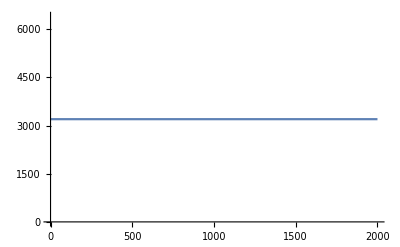
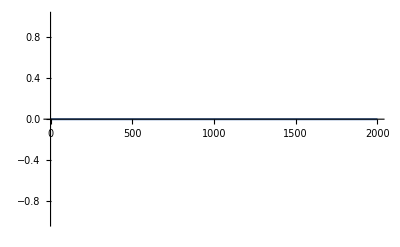
<|{2,1->2}→-Graphics-,{ex81,2->ex81}→-Graphics-,{1,en80->1}→-Graphics-,{1,1->2}→-Graphics-,{2,2->ex81}→-Graphics-,{en80,en80->1}→-Graphics-|>

```mathematica
Function[a,ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-a/(m^(1-alpha)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]]/@jv
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will always retrieve the most up - to - date values.